```mathematica
$Assumptions = {Δ ∈ Reals,Δ < 0, t ∈ Reals, ϕ ∈ Reals, θ ∈ Reals, z ∈ Integers, q ∈ Reals, α ∈ Reals}
```

{Δ∈ℝ,Δ<0,t∈ℝ,ϕ∈ℝ,θ∈ℝ,z∈ℤ,q∈ℝ,α∈ℝ}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
lm1 = 1/Sqrt[3] * {1, ω^2, ω}
l0 = 1/Sqrt[3] * {1, 1, 1}
lp1 = 1/Sqrt[3] * {1, ω, ω^2}
```

{1/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3),ⅇ^((2 ⅈ π)/3)/(√3)}

{1/(√3),1/(√3),1/(√3)}

{1/(√3),ⅇ^((2 ⅈ π)/3)/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3)}

```mathematica
nm1= FullSimplify[1/Sqrt[2]*l0 - 1/2(Exp[-I θ] lp1 - Exp[I θ] lm1)]
n0= FullSimplify[1/Sqrt[2](Exp[-I θ] lp1 + Exp[I θ] lm1)]
np1= FullSimplify[1/Sqrt[2]*l0 + 1/2(Exp[-I θ] lp1 - Exp[I θ] lm1)]
```

{1/(√6)+(ⅈ Sin[θ])/(√3),1/6 (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ]),1/6 (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])}

{√(2/3) Cos[θ],(-Cos[θ]+√3 Sin[θ])/(√6),-(Cos[θ]+√3 Sin[θ])/(√6)}

{1/(√6)-(ⅈ Sin[θ])/(√3),1/6 (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ]),1/6 (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])}

```mathematica
ϵ = Sqrt[6] * q * α
Δt = 3/2 Δ
```

√6 q α

(3 Δ)/2

```mathematica
pnmz = Sqrt[ϵ^2+Δt^2]
```

√(6 q^2 α^2+(9 Δ^2)/4)

```mathematica
pm1 =FullSimplify[ 1/Sqrt[2 *pnmz * (ϵ + pnmz)] * (-Δt*np1 +  (ϵ + pnmz) * nm1)]
p0 = FullSimplify[n0]
pp1 = FullSimplify[1/Sqrt[2 *pnmz * (ϵ + pnmz)] * (Δt*nm1 +  (ϵ + pnmz) * np1)]
```

{(4 √3 q α-3 √2 Δ+√6 √(8 q^2 α^2+3 Δ^2)+2 ⅈ (2 √6 q α+3 Δ+√(24 q^2 α^2+9 Δ^2)) Sin[θ])/(6 √(6 Δ^2+4 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])-1/4 Δ (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])-1/4 Δ (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))}

{√(2/3) Cos[θ],(-Cos[θ]+√3 Sin[θ])/(√6),-(Cos[θ]+√3 Sin[θ])/(√6)}

{(4 √3 q α+3 √2 Δ+√6 √(8 q^2 α^2+3 Δ^2)-2 ⅈ (2 √6 q α-3 Δ+√(24 q^2 α^2+9 Δ^2)) Sin[θ])/(6 √(6 Δ^2+4 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/4 Δ (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])+1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2)))),(√2 (1/4 Δ (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])+1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))}

```mathematica
C1m = FullSimplify[Part[pm1, 1]]
C3m = FullSimplify[Part[pm1, 2]]
C5m = FullSimplify[Part[pm1, 3]]
```

(4 √3 q α-3 √2 Δ+√6 √(8 q^2 α^2+3 Δ^2)+2 ⅈ (2 √6 q α+3 Δ+√(24 q^2 α^2+9 Δ^2)) Sin[θ])/(6 √(6 Δ^2+4 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))

(√2 (1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6-3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])-1/4 Δ (√6+3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))

(√2 (1/6 (√6 q α+√(6 q^2 α^2+(9 Δ^2)/4)) (√6+3 ⅈ Cos[θ]-ⅈ √3 Sin[θ])-1/4 Δ (√6-3 ⅈ Cos[θ]+ⅈ √3 Sin[θ])))/(√(9 Δ^2+6 q α (4 q α+√(16 q^2 α^2+6 Δ^2))))

```mathematica
q = 1
Δ = -1
α =3
```

1

-1

3

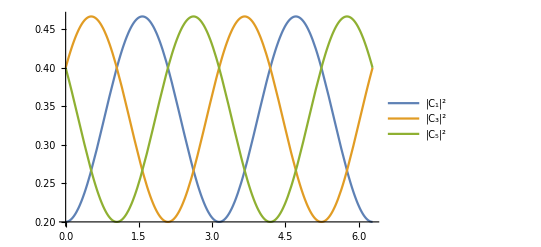

```mathematica
Plot[{C1m*Conjugate[C1m], C3m * Conjugate[C3m], C5m * Conjugate[C5m]}, {θ, 0, 2 π}, PlotLegends->{"|C_1|^2","|C_3|^2", "|C_5|^2" }]
```

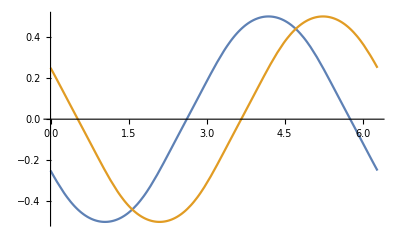

```mathematica
Plot[{Arg[C3m/C1m]*1/π,Arg[C5m/C1m]*1/π}, {θ, 0, 2 π}]
```

```mathematica
Clear[α, q, Δ, θ]
```

```mathematica
Series[FullSimplify[ComplexExpand[Conjugate[C1m]*C1m]], {q, 0, 2}]
```

1/3-(2 (α^2 Cos[2 θ]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[ComplexExpand[Conjugate[C3m]*C3m]], {q, 0, 2}]
```

1/3+((α^2 Cos[2 θ]+√3 α^2 Sin[2 θ]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[ComplexExpand[Conjugate[C5m]*C5m]], {q, 0, 2}]
```

1/3+((α^2 Cos[2 θ]-√3 α^2 Sin[2 θ]) q^2)/(9 Δ^2)+O[q]^3